# ImStat

Statistics of image collection

## Setup and data collection

## Config

Source folder for JPG files:

```mathematica
imageDir="/media/superraid/images/images/";
```

Nr of raw files:

```mathematica
nrRawFiles=FileNames["*.CR2",imageDir,∞]//Length
```

9981

```mathematica
jpgFileNames=FileNames["*.jpg"|"*.JPG",imageDir,∞];
```

Number of images found:

```mathematica
nrJpgFiles=Length[jpgFileNames]
```

3955

Folder for local data storage:

```mathematica
dataDir=FileNameJoin[{NotebookDirectory[],"dataStorage"}]
```

/home/malte/dev/imStat/dataStorage

```mathematica
CreateDirectory[dataDir]
```

/home/malte/dev/imStat/dataStorage

## Retrieve mini JPG files and basic data

Compute data file name from original path, making sure that no collisions will occur:

```mathematica
(Union[Hash[#,"CRC32"]&/@jpgFileNames]//Length)==nrJpgFiles
```

True

```mathematica
storageFile[path_]:=FileNameJoin[{dataDir,ToString[Hash[path,"CRC32"]]<>".dst"}];
```

```mathematica
storageFileImg[path_]:=FileNameJoin[{dataDir,ToString[Hash[path,"CRC32"]]<>".jpg"}];
```

Fetch original image and save data into data file:

```mathematica
createData[path_]/;FileExistsQ[storageFile[path]]=Null;
```

```mathematica
createData[path_]:=Module[{img,dimensions,smallImg,aperture,bitDepth,orientation,colorSpace,date,exposure,focalLength,imageSize,iso,manufacturer,model,exifData},
exifData=Import[path,{{"Aperture","BitDepth","CameraTopOrientation","ColorSpace","Date","Exposure","FocalLength","ImageSize","ISOSpeed","Manufacturer","Model"}}];
If[!MatchQ[exifData,{_,_,_,_String,{_,_,_,_,_,_},_,_,{_,_},_,_String,_String}],
Return[$Failed];
];
img=Import[path];
dimensions=ImageDimensions[img];
smallImg=ImageResize[img,{300},Resampling->"Bilinear"];
Put[{dimensions,exifData},storageFile[path]];
Export[storageFileImg[path],smallImg];
]
```

File size:

```mathematica
fileSizes={#,FileByteCount[#]}&/@jpgFileNames;
```

```mathematica
Put[fileSizes,FileNameJoin[{dataDir,"fileSizes.dst"}]];
```

Retrieving file sizes:

```mathematica
fileSizes=Get[FileNameJoin[{dataDir,"fileSizes.dst"}]];
```

Fetch data in order of preference {memory, data file}:

```mathematica
ClearAll[getData];
getData[path_]/;FileExistsQ[storageFile[path]]:=getData[path]={Import[storageFileImg[path]],Get[storageFile[path]]}
```

```mathematica
getData[_]:=$Failed
```

Accessor functions for properties:

```mathematica
getData[path_,"Date"]:=getData[path][[2,2,5]]
```

```mathematica
getData[path_,"Orientation"]:=getData[path][[2,2,3]]
```

```mathematica
getData[path_,"Camera"]:=getData[path][[2,2,10;;11]]
```

```mathematica
getData[path_,"Aperture"]:=getData[path][[2,2,1]]
```

```mathematica
getData[path_,"BitDepth"]:=getData[path][[2,2,2]]
```

```mathematica
getData[path_,"ColorSpace"]:=getData[path][[2,2,4]]
```

```mathematica
getData[path_,"Exposure"]:=getData[path][[2,2,6]]
```

```mathematica
getData[path_,"FocalLength"]:=getData[path][[2,2,7]]
```

```mathematica
getData[path_,"ImageSize"]:=getData[path][[2,1]]
```

## Retrieve image data

```mathematica
Monitor[
ParallelDo[createData[jpgFileNames[[i]]],{i,Length[jpgFileNames]}],
Refresh[
ProgressIndicator[Length@FileNames["*",dataDir],{0,2Length[jpgFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
]
```

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

```mathematica
goodFileNames=Select[jpgFileNames,FileExistsQ[storageFile[#]]&&FileExistsQ[storageFileImg[#]]&];
```

## Results

## Number of images taken

```mathematica
nrJpg=Length[jpgFileNames]
```

3955

```mathematica
nrGood=Length[goodFileNames]
```

3686

```mathematica
nrNotGood=nrJpg-nrGood
```

269

```mathematica
PieChart[{nrGood,nrNotGood},ChartLabels->{"","No data"}]
```

-Graphics-

## Images taken over time

```mathematica
getData[goodFileNames[[1]],"Date"]
```

{2007,12,23,17,14,56}

```mathematica
imageDates=Monitor[
Table[getData[goodFileNames[[i]],"Date"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
oldestYear=Min@imageDates[[All,1]]
```

2006

```mathematica
newestYear=Max@imageDates[[All,1]]
```

2012

```mathematica
nrTakenTime=Join@@Table[{{y,m},Length@Cases[imageDates,{y,m,d_,h_,mi_,s_}]},{y,oldestYear,newestYear},{m,1,12}]
```

{{{2006,1},0},{{2006,2},0},{{2006,3},0},{{2006,4},0},{{2006,5},0},{{2006,6},0},{{2006,7},0},{{2006,8},0},{{2006,9},0},{{2006,10},0},{{2006,11},0},{{2006,12},6},{{2007,1},0},{{2007,2},8},{{2007,3},22},{{2007,4},138},{{2007,5},44},{{2007,6},42},{{2007,7},90},{{2007,8},41},{{2007,9},244},{{2007,10},170},{{2007,11},114},{{2007,12},166},{{2008,1},286},{{2008,2},202},{{2008,3},261},{{2008,4},91},{{2008,5},253},{{2008,6},190},{{2008,7},233},{{2008,8},429},{{2008,9},0},{{2008,10},2},{{2008,11},1},{{2008,12},26},{{2009,1},2},{{2009,2},3},{{2009,3},0},{{2009,4},20},{{2009,5},3},{{2009,6},5},{{2009,7},8},{{2009,8},0},{{2009,9},0},{{2009,10},6},{{2009,11},0},{{2009,12},2},{{2010,1},0},{{2010,2},0},{{2010,3},0},{{2010,4},0},{{2010,5},3},{{2010,6},0},{{2010,7},1},{{2010,8},1},{{2010,9},0},{{2010,10},7},{{2010,11},6},{{2010,12},1},{{2011,1},151},{{2011,2},0},{{2011,3},0},{{2011,4},249},{{2011,5},10},{{2011,6},9},{{2011,7},1},{{2011,8},0},{{2011,9},3},{{2011,10},35},{{2011,11},0},{{2011,12},0},{{2012,1},0},{{2012,2},0},{{2012,3},60},{{2012,4},8},{{2012,5},0},{{2012,6},33},{{2012,7},0},{{2012,8},0},{{2012,9},0},{{2012,10},0},{{2012,11},0},{{2012,12},0}}

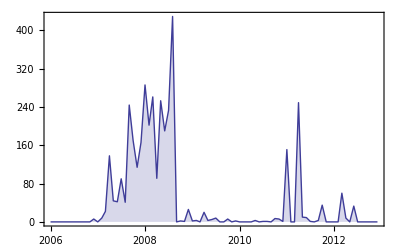

```mathematica
DateListPlot[nrTakenTime,Joined->True,PlotRange->All,Filling->Axis,GridLines->None]
```

## Camera models

```mathematica
getData[goodFileNames[[1]],"Camera"]
```

{Canon,Canon EOS Kiss Digital N}

```mathematica
imageCameras=Monitor[
Table[getData[goodFileNames[[i]],"Camera"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
{cameraLabel,cameraData}=Transpose@Tally@imageCameras
```

{{{Canon,Canon EOS Kiss Digital N},{Sony Ericsson,K800i},{Canon,Canon EOS 40D},{NIKON CORPORATION,NIKON D3000},{Canon,Canon EOS 650D}},{2517,1074,4,66,25}}

```mathematica
formatLabel[{"Canon","Canon EOS Kiss Digital N"}]="Canon 350D";
formatLabel[{"Sony Ericsson","K800i"}]="Sony Ericsson K800i";
formatLabel[{"Canon","Canon EOS 40D"}]="Canon 40D";
formatLabel[{"NIKON CORPORATION","NIKON D3000"}]="Nikon D3000";
formatLabel[{"Canon","Canon EOS 650D"}]="Canon 650D";
```

```mathematica
PieChart[cameraData,ChartLabels->Placed[formatLabel/@cameraLabel,"RadialCallout"],ImagePadding->50,SectorOrigin->π 10.1/5]
```

-Graphics-

```mathematica
PieChart[cameraData,ChartLegends->formatLabel/@cameraLabel]
```

-Graphics--Graphics- | Canon 350D
-Graphics- | Sony Ericsson K800i
-Graphics- | Canon 40D
-Graphics- | Nikon D3000
-Graphics- | Canon 650D

```mathematica
gatheredData=GatherBy[getData/@goodFileNames,#[[2,2,-1]]&];
```

```mathematica
gatheredAbsoluteData=(AbsoluteTime/@#[[All,2,2,5]])&/@gatheredData;
```

```mathematica
gatheredCameras=((#[[All,2,2,-2;;-1]])&/@gatheredData)[[All,1]]
```

{{Canon,Canon EOS Kiss Digital N},{Sony Ericsson,K800i},{Canon,Canon EOS 40D},{NIKON CORPORATION,NIKON D3000},{Canon,Canon EOS 650D}}

```mathematica
cameraMinMaxTimes={Min[#],Max[#]}&/@gatheredAbsoluteData
```

{{3407418896,3549444936},{3374342953,3424212073},{3448542854,3543403300},{3541055433,3543405998},{3549721924,3550052918}}

```mathematica
minCameraTime=Min[cameraMinMaxTimes]
```

3374342953

```mathematica
maxCameraTime=Max[cameraMinMaxTimes]
```

3550052918

```mathematica
yearTickFn[min_,max_]:=Table[{i,DateList[i+minCameraTime][[1]]},{i,min,max,3 10^7}]
```

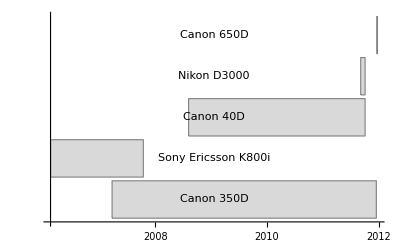

```mathematica
BarChart[{#[[1]]-minCameraTime,#[[2]]-#[[1]],maxCameraTime-#[[2]]}&/@cameraMinMaxTimes,ChartLayout->"Stacked",ChartStyle->{Directive[Transparent,EdgeForm[None]],Directive[LightGray,EdgeForm[Gray]],Directive[Transparent,EdgeForm[None]]},BarOrigin->Left,Axes->{True,False},ChartLabels->{None,Placed[formatLabel/@gatheredCameras,Center],None},Ticks->{yearTickFn,None}]
```

## Aperture

```mathematica
getData[goodFileNames[[1]],"Aperture"]
```

4

```mathematica
imageAperture=Monitor[
Table[getData[goodFileNames[[i]],"Aperture"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

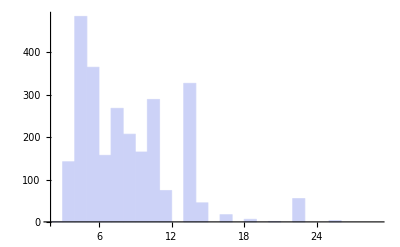

```mathematica
Histogram[imageAperture]
```

```mathematica
Manipulate[Graphics[{EdgeForm[LightGray],Gray,Table[Polygon[{{Cos[t],Sin[t]},{Cos[t-o],Sin[t-o]}/d,{Cos[t+2Pi/6],Sin[t+2Pi/6]},Sequence@@Table[{Cos[x],Sin[x]},{x,t+2Pi/6,t,-0.1}]}],{t,0,2Pi,2Pi/6}]},ImageSize->400],{d,1,10},{o,0,2Pi}]
```

```mathematica
closedAperture=With[{d=4.27,o=0.819513},Graphics[{EdgeForm[LightGray],Gray,Table[Polygon[{{Cos[t],Sin[t]},{Cos[t-o],Sin[t-o]}/d,{Cos[t+(2 π)/6],Sin[t+(2 π)/6]},Sequence@@Table[{Cos[x],Sin[x]},{x,t+(2 π)/6,t,-0.1}]}],{t,0,2 π,(2 π)/6}]},ImageSize->60]]
```

-Graphics-

```mathematica
openAperture=With[{d=1.12,o=0.160796},Graphics[{EdgeForm[LightGray],Gray,Table[Polygon[{{Cos[t],Sin[t]},{Cos[t-o],Sin[t-o]}/d,{Cos[t+(2 π)/6],Sin[t+(2 π)/6]},Sequence@@Table[{Cos[x],Sin[x]},{x,t+(2 π)/6,t,-0.1}]}],{t,0,2 π,(2 π)/6}]},ImageSize->60]]
```

-Graphics-

```mathematica
SmoothHistogram[imageAperture,AxesOrigin->{0,0},Axes->{True,False},PlotRangePadding->{{10,Automatic},Automatic},Filling->Axis,Epilog->{Inset[openAperture,{-3,Center}],Inset[closedAperture,{27,Center}]}]
```

-Graphics-

## Time of day taken

```mathematica
timeOfDayToSeconds[{h_,m_,s_}]:=s+(m+h*60)*60
```

```mathematica
timeOfDayToHour[{h_,m_,s_}]:=h
```

```mathematica
Tally[timeOfDayToHour/@imageDates[[All,4;;]]]
```

{{17,187},{18,196},{22,325},{13,255},{14,252},{15,248},{20,467},{19,183},{23,103},{0,156},{3,30},{4,37},{5,26},{6,23},{12,236},{21,370},{16,193},{1,71},{10,75},{11,183},{8,7},{9,21},{2,31},{7,11}}

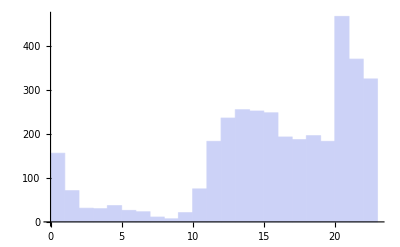

```mathematica
Histogram[timeOfDayToHour/@imageDates[[All,4;;]],Axes->{True,False}]
```

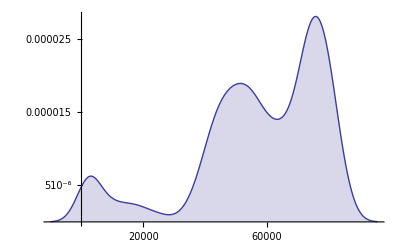

```mathematica
SmoothHistogram[timeOfDayToSeconds/@imageDates[[All,4;;]],Axes->{True,False},Filling->Axis]
```

## Exposure

```mathematica
getData[goodFileNames[[1]],"Exposure"]
```

1/60

```mathematica
imageExposure=Monitor[
Table[getData[goodFileNames[[i]],"Exposure"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Max[imageExposure]
```

139

```mathematica
Min[imageExposure]
```

1/6400

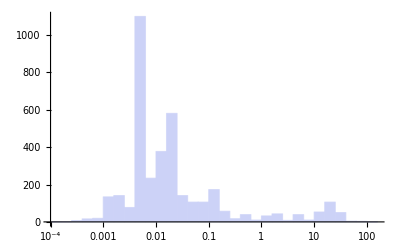

```mathematica
Histogram[imageExposure,"Log",Axes->{True,False}]
```

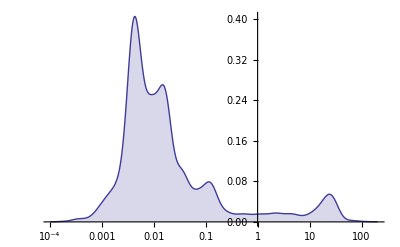

```mathematica
SmoothHistogram[Log@imageExposure,Ticks->{Charting`ScaledTicks[{Log,Exp}],Automatic},Axes->{True,False},Filling->Axis]
```

## Focal length

```mathematica
getData[goodFileNames[[1]],"FocalLength"]
```

28.

```mathematica
imageFocalLength=Monitor[
Table[getData[goodFileNames[[i]],"FocalLength"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Max[imageFocalLength]
```

Max[300.,None]

```mathematica
Min[imageFocalLength]
```

Min[17.,None]

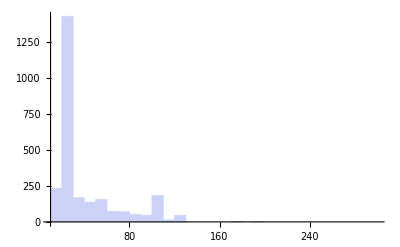

```mathematica
Histogram[imageFocalLength,Axes->{True,False}]
```

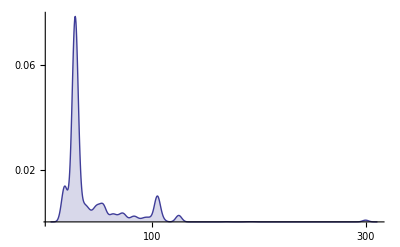

```mathematica
SmoothHistogram[imageFocalLength,Axes->{True,False},Filling->Axis]
```

## Image size

```mathematica
getData[goodFileNames[[1]],"ImageSize"]
```

{3456,2304}

```mathematica
imageSizes=Monitor[
Table[getData[goodFileNames[[i]],"ImageSize"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
talliedImageSizes=Tally[imageSizes];
```

```mathematica
miniTalliesImageSizes=Cases[talliedImageSizes,{{_,_},a_}/;a>1]
```

{{{3456,2304},853},{{2304,3456},516},{{1215,1506},3},{{1506,1215},2},{{3131,1746},2},{{2944,1847},2},{{1689,2261},2},{{2304,1600},2},{{2736,1615},2},{{2241,3362},2},{{2064,3096},2},{{2730,1820},2},{{2215,1477},2},{{2175,1450},2},{{200,200},2},{{2012,1341},2},{{2055,3083},2},{{2021,3031},2},{{1695,2542},2},{{1449,2174},2},{{1536,2304},9},{{2089,3134},4},{{1901,2851},3},{{2812,1874},2},{{2604,1736},2},{{2770,1847},3},{{3036,2024},2},{{2740,1827},2},{{2817,1878},4},{{3242,2161},2},{{2128,3193},2},{{2380,1587},2},{{1826,2739},2},{{3018,2012},2},{{2882,1922},2},{{2515,1677},2},{{3123,2082},2},{{2507,1671},3},{{1947,2920},2},{{3401,2267},2},{{3166,2111},2},{{3374,2249},2},{{2137,1424},2},{{1511,1007},2},{{2483,1656},2},{{3200,2133},2},{{1783,2674},2},{{2048,1536},790},{{3262,2175},3},{{3304,2202},2},{{2224,3336},2},{{2198,3297},2},{{2581,1721},2},{{3280,2186},2},{{1024,683},575},{{1876,2814},2},{{2367,1578},2},{{1680,1120},2},{{2270,1513},2},{{3474,2314},14},{{1861,2791},2},{{2084,3126},2},{{1411,2117},2},{{3311,2208},2},{{1677,2515},2},{{1280,1920},2},{{3256,2171},2},{{2820,1880},2},{{3273,2182},3},{{2077,3115},2},{{3309,2206},2},{{2249,3374},2},{{2093,3140},2},{{3872,2592},34},{{2592,3872},24},{{5184,3456},8},{{3456,5184},3},{{1536,2048},281}}

```mathematica
maxImgSizeNr=Max[talliedImageSizes[[All,2]]]
```

853

```mathematica
Sort[miniTalliesImageSizes,#1[[2]]>#2[[2]]&]
```

{{{3456,2304},853},{{2048,1536},790},{{1024,683},575},{{2304,3456},516},{{1536,2048},281},{{3872,2592},34},{{2592,3872},24},{{3474,2314},14},{{1536,2304},9},{{5184,3456},8},{{2817,1878},4},{{2089,3134},4},{{3456,5184},3},{{3273,2182},3},{{3262,2175},3},{{2507,1671},3},{{2770,1847},3},{{1901,2851},3},{{1215,1506},3},{{2093,3140},2},{{2249,3374},2},{{3309,2206},2},{{2077,3115},2},{{2820,1880},2},{{3256,2171},2},{{1280,1920},2},{{1677,2515},2},{{3311,2208},2},{{1411,2117},2},{{2084,3126},2},{{1861,2791},2},{{2270,1513},2},{{1680,1120},2},{{2367,1578},2},{{1876,2814},2},{{3280,2186},2},{{2581,1721},2},{{2198,3297},2},{{2224,3336},2},{{3304,2202},2},{{1783,2674},2},{{3200,2133},2},{{2483,1656},2},{{1511,1007},2},{{2137,1424},2},{{3374,2249},2},{{3166,2111},2},{{3401,2267},2},{{1947,2920},2},{{3123,2082},2},{{2515,1677},2},{{2882,1922},2},{{3018,2012},2},{{1826,2739},2},{{2380,1587},2},{{2128,3193},2},{{3242,2161},2},{{2740,1827},2},{{3036,2024},2},{{2604,1736},2},{{2812,1874},2},{{1449,2174},2},{{1695,2542},2},{{2021,3031},2},{{2055,3083},2},{{2012,1341},2},{{200,200},2},{{2175,1450},2},{{2215,1477},2},{{2730,1820},2},{{2064,3096},2},{{2241,3362},2},{{2736,1615},2},{{2304,1600},2},{{1689,2261},2},{{2944,1847},2},{{3131,1746},2},{{1506,1215},2}}

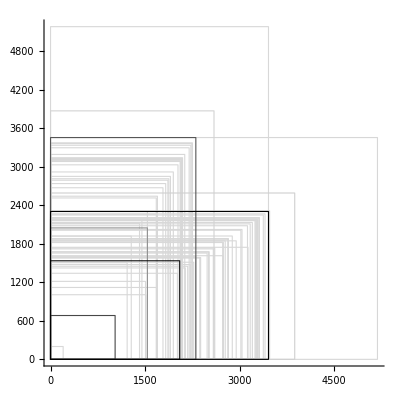

```mathematica
Graphics[{FaceForm[None],EdgeForm[Darker[LightGray,(#[[2]]/maxImgSizeNr)]],Rectangle[{0,0},#[[1]]]}&/@Sort[miniTalliesImageSizes,#1[[2]]<#2[[2]]&],Axes->True,AxesStyle->Gray,AspectRatio->1]
```

## ISO

## Image colors over time

## Orientations [use image sizes]

```mathematica
imageOrientations=Monitor[
Table[getData[goodFileNames[[i]],"Orientation"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
{orientLabel,orientNr}=Transpose@Tally[Cases[imageOrientations,Except[None]]]
```

{{Right,Top,Left},{5,1798,9}}

```mathematica
PieChart[orientNr,ChartLabels->orientLabel]
```

-Graphics-

## Memory used

```mathematica
Total@fileSizes[[All,2]]
```

6114153844

## Problematic

## Bit depth [boring]

```mathematica
getData[goodFileNames[[1]],"BitDepth"]
```

8

```mathematica
imageBitDepth=Monitor[
Table[getData[goodFileNames[[i]],"BitDepth"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Tally@imageBitDepth
```

{{8,3686}}

## Flash [no data]

## Color space [boring, possibly incorrect]

```mathematica
getData[goodFileNames[[1]],"ColorSpace"]
```

RGBColor

```mathematica
imageColorSpace=Monitor[
Table[getData[goodFileNames[[i]],"ColorSpace"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Tally@imageColorSpace
```

{{RGBColor,3676},{Grayscale,10}}